Berechnung für Praktikumsversuch Quantisierter Leitwert
In diesem Notebook importieren wir die Daten aus dem Versuch und packen sie in handhabbarere Form (Listen). Dann fitten wir die Box-Daten linear und nutzen den Anstieg um die Leitwerte zu korrigieren. Dann erstellen wir Plots der Messungen mit quantisiertem Leitwert. Es werden auch die vom Betreuer gegebenen Daten veranschaulicht, allerdings ohne Korrektur, da hierzu keine weiteren Daten vorlagen.

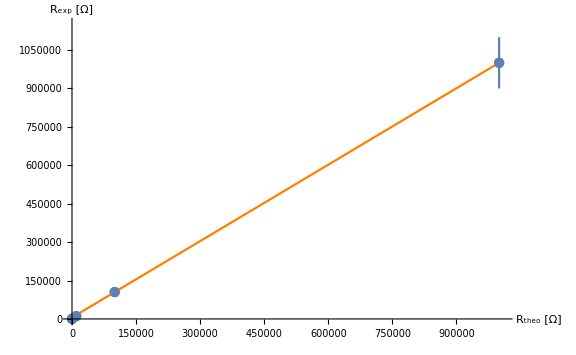

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5424.55 | 311.045 | 17.4398 | 0.000410896
x | 0.994396 | 0.000326228 | 3048.16 | 7.78678×10^-11

```mathematica
(* Lade ErrorBar Package *)
Needs["ErrorBarPlots`"]

(* Importiere Daten von Widerstandsbox *)
Ohm100 =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100ohm.dat","FieldSeparators"->","];
Ohm1k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1000ohm.dat","FieldSeparators"->","];
Ohm10k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/10kOhm.dat","FieldSeparators"->","];
Ohm100k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100kOhm.dat","FieldSeparators"->","];
Ohm1M =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1MOhm.dat","FieldSeparators"->","];

(* Berechne Leitwert aus Mittel der Widerstände (6 Messwerte) *)
a =Sum[1/Sqrt[Ohm100[[n,1]]^2+Ohm100[[n,2]]^2],{n,Length[Ohm100]}]/Length[Ohm100];
b =Sum[1/Sqrt[Ohm1k[[n,1]]^2+Ohm1k[[n,2]]^2],{n,Length[Ohm1k]}]/Length[Ohm1k];
c =Sum[1/Sqrt[Ohm10k[[n,1]]^2+Ohm10k[[n,2]]^2],{n,Length[Ohm10k]}]/Length[Ohm10k];
d =Sum[1/Sqrt[Ohm100k[[n,1]]^2+Ohm100k[[n,2]]^2],{n,Length[Ohm100k]}]/Length[Ohm100k];
e =Sum[1/Sqrt[Ohm1M[[n,1]]^2+Ohm1M[[n,2]]^2],{n,Length[Ohm1M]}]/Length[Ohm1M];

(* Daten + Fehler  10fach für Sichtbarkeit*)
data = {{100,a},{1000,b},{10000,c},{100000,d},{1000000,e}};
errors = {0.1,1,10,1000,10000};
dataerror = Transpose[{data[[All,1]],data[[All,2]],10*errors}];

(* linearer Fit + Plot *)
lm = LinearModelFit[data,x,x,Weights->errors];
PlotBox=Show[ListPlot[data,PlotRange->{{0,1.01*10^6},{0,1.15*10^6}}],Plot[lm[x],{x,0,1000000},PlotStyle->Orange],ErrorListPlot[dataerror],ImageSize->Large, AxesLabel->{"   R_theo [Ω]","R_exp [Ω]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]

(* Exportiere als .eps *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/box.eps",PlotBox];

(* Parameter des Fits *)
lm["ParameterTable"]

(* Steigung des Fit *)
Slope=Last[lm["BestFitParameters"]];
```

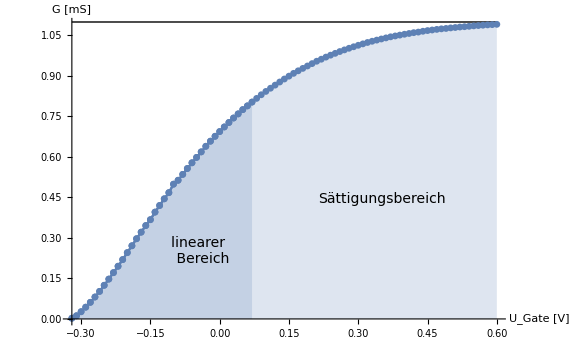

```mathematica
(* Importiere Struktur G *)
G = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/G.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
(* korrigiere Leitwerte um Abweichung aus Widerstandsbox G -> Slope^-1*G *)
(* rechne *1000 für Darstellung in mS *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,G[[n,1]]],{n,Length[G]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,1000*1/Slope*Sqrt[G[[n,2]]^2 + G[[n,3]]^2  ]],{n,Length[G]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot mit Bereichen und Sättigungsleitwert *)
PlotG =Show[
ListPlot[data2,Joined->True,PlotMarkers->{Automatic,7},Filling->Axis], 
ListPlot[data2[[1;;40]],Joined->True,PlotMarkers->{Automatic,7},Filling->Axis],
AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate [V]","G [mS]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],
Epilog->{ 
Line[{{Min[Spannungen],1.1},{0.6,1.1}}],Text[Style["Sättigungsbereich",14],Scaled[{0.72,0.41}]],Text[Style["linearer \n Bereich",14],Scaled[{0.31,0.24}]]
}
]

(* Exportiere als .eps *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/g.eps",PlotG];
```

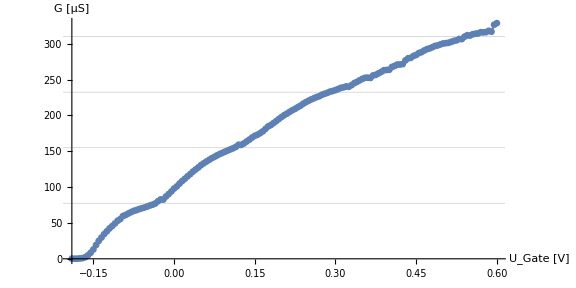

```mathematica
(* Importiere Struktur I*)
J= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/QL_I.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
(* korrigiere Leitwerte um Abweichung aus Widerstandsbox G -> Slope^-1*G *)
(* Verwende Formel Subscript[G, n]=1/(Subscript[G, J]^-1-Subscript[R, S]) für Leitwerte *)
(* rechne *1000 für Darstellung in mS *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,J[[n,1]]],{n,Length[J]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,1000^2*1/(1/(1/Slope*Sqrt[J[[n,2]]^2 + J[[n,3]]^2  ])-(1/0.0012))],{n,Length[J]}];
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot mit GridLines in Vielfachen von 2e^2/h*)
PlotJ = ListPlot[data2,Joined->True,PlotMarkers->{Automatic,7}, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate [V]","G [μS]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],GridLines->{None,{77.48,2*77.48,3*77.48,4*77.48}},AspectRatio->1/2]

(* Exportiere als .eps *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/j.eps",PlotJ];
```

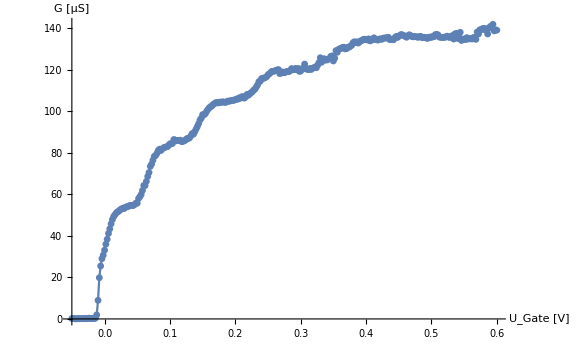

```mathematica
(* Importiere Struktur L (Daten von Betreuer) *)
L = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/L.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
(* korrigiere Leitwerte um Abweichung aus Widerstandsbox G -> Slope^-1*G *)
(* rechne *1000 für Darstellung in mS *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,L[[n,1]]],{n,Length[L]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,1000^2*1/Slope*Sqrt[L[[n,2]]^2 + L[[n,3]]^2  ]],{n,Length[L]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotL = ListPlot[data2,Joined->True,PlotMarkers->{Automatic,7}, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate [V]","G [μS]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]

(* Exportiere als .eps *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/l.eps",PlotL];
```

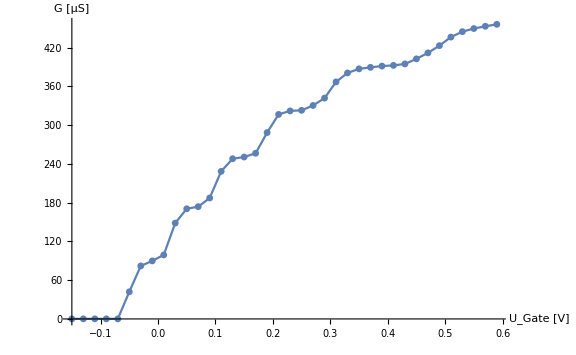

```mathematica
(* Importiere Struktur L_fein (Daten von Versuchsbetreuer) *)
Lfein= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/Lfein.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
(* korrigiere Leitwerte um Abweichung aus Widerstandsbox G -> Slope^-1*G *)
(* rechne *1000 für Darstellung in mS *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,Lfein[[n,1]]],{n,Length[Lfein]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,1000^2*1/Slope*Sqrt[Lfein[[n,2]]^2 + Lfein[[n,3]]^2  ]],{n,Length[Lfein]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotLfein = ListPlot[data2,Joined->True,PlotMarkers->{Automatic,7}, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate [V]","G [μS]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]

(* Exportiere als .eps *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/lfein.eps",PlotLfein];
```